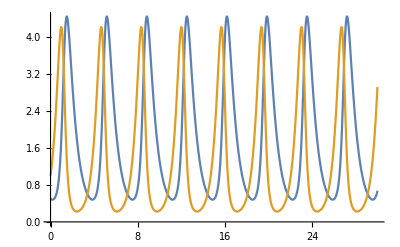

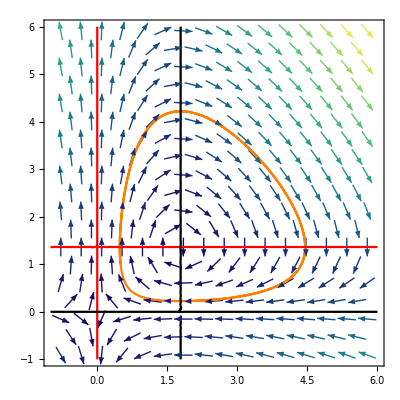

{{0,0},{25/14,15/11}}

```mathematica
α=15/10;
β=11/10;
γ=25/10;
δ=14/10;
{Subscript[s, 1][t_],Subscript[s, 2][t_]}=NDSolveValue[
{Subscript[x, 1]'[t]==-α Subscript[x, 1][t]+β Subscript[x, 1][t]Subscript[x, 2][t],
Subscript[x, 2]'[t]==γ Subscript[x, 2][t]-δ Subscript[x, 1][t]Subscript[x, 2][t],
Subscript[x, 1][0]==0.5,
Subscript[x, 2][0]==1.0},
{Subscript[x, 1][t],Subscript[x, 2][t]},
{t,0,30}];
Plot[{Subscript[s, 1][t],Subscript[s, 2][t]},{t,0,30}]
Show[VectorPlot[
{-α Subscript[x, 1]+β Subscript[x, 1] Subscript[x, 2],
γ Subscript[x, 2]-δ Subscript[x, 1] Subscript[x, 2]},
{Subscript[x, 1],-1,6},{Subscript[x, 2],-1,6},
VectorColorFunction->"BlueGreenYellow"],
ParametricPlot[{Subscript[s, 1][t],Subscript[s, 2][t]},{t,0,6},PlotStyle->Orange],
ContourPlot[{-α Subscript[x, 1]+β Subscript[x, 1] Subscript[x, 2]==0,γ Subscript[x, 2]-δ Subscript[x, 1] Subscript[x, 2]==0},
{Subscript[x, 1],-1,6},{Subscript[x, 2],-1,6},
ContourStyle->{Red,Black}]]
SolveValues[{-α Subscript[x, 1]+β Subscript[x, 1] Subscript[x, 2]==0,γ Subscript[x, 2]-δ Subscript[x, 1] Subscript[x, 2]==0},{Subscript[x, 1],Subscript[x, 2]}]
```

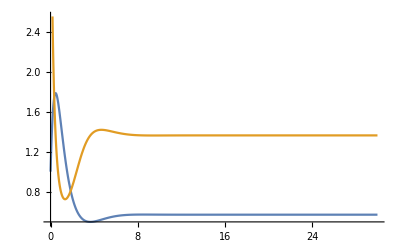

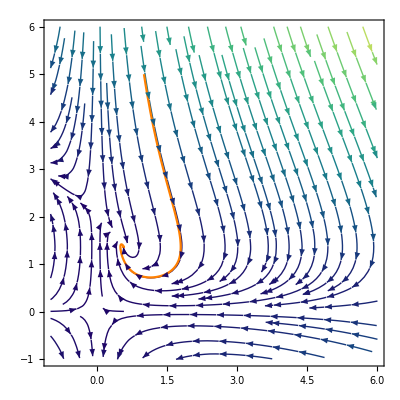

```mathematica
α=1.5;
β=1.1;
γ=2.5;
δ=1.4;
κ=0.5;
{Subscript[s, 1][t_],Subscript[s, 2][t_]}=NDSolveValue[
{Subscript[x, 1]'[t]==-α Subscript[x, 1][t]+β Subscript[x, 1][t]Subscript[x, 2][t],
Subscript[x, 2]'[t]==γ (1-κ Subscript[x, 2][t])Subscript[x, 2][t]-δ Subscript[x, 1][t]Subscript[x, 2][t],
Subscript[x, 1][0]==1,
Subscript[x, 2][0]==5},
{Subscript[x, 1][t],Subscript[x, 2][t]},
{t,0,30}];
Plot[{Subscript[s, 1][t],Subscript[s, 2][t]},{t,0,30}]
Show[StreamPlot[
{-α Subscript[x, 1]+β Subscript[x, 1] Subscript[x, 2],
γ (1-κ Subscript[x, 2])Subscript[x, 2]-δ Subscript[x, 1] Subscript[x, 2]},
{Subscript[x, 1],-1,6},{Subscript[x, 2],-1,6},
StreamColorFunction->"BlueGreenYellow"],
ParametricPlot[
{Subscript[s, 1][t],Subscript[s, 2][t]},
{t,0,30},
PlotStyle->Orange]]
```